```mathematica
P[s] := (koffu*kuon)/((s+kuon)*(s+koffu+c*kbon)-c*kbon*kuon)
```

```mathematica
d2P[s]:=FullSimplify[D[P[s], {s,2}]]
```

```mathematica
With[{s=0}, Evaluate[d2P[s]]] - (1/koffu + 1/kuon + c*kbon/(koffu*kuon))^2
```

-(1/koffu+1/kuon+(c kbon)/(koffu kuon))^2+(2 (c kbon kuon-(c kbon+koffu) kuon+(c kbon+koffu+kuon)^2))/(koffu^2 kuon^2)

```mathematica
FullSimplify[%]
```

((c kbon+koffu)^2+2 c kbon kuon+kuon^2)/(koffu^2 kuon^2)

```mathematica
p[c]=FullSimplify[InverseLaplaceTransform[P[s],s,t]]
```

(ⅇ^(-1/2 (c kbon+koffu+kuon+√(-4 koffu kuon+(c kbon+koffu+kuon)^2)) t) (-1+ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t)) koffu kuon)/(√(-4 koffu kuon+(c kbon+koffu+kuon)^2))

```mathematica
psimpl = Simplify[p[c],{A==koffu kuon,B==c kbon+koffu+kuon,D==-4 koffu kuon+(c kbon+koffu+kuon)^2}]
```

(A ⅇ^(-1/2 (B+√D) t) (-1+ⅇ^(√D t)))/(√D)

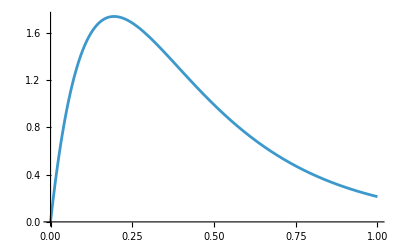

```mathematica
Plot[With[{c=10, kbon=0.0888,koffu=5, kuon=5 }, Evaluate[p[c]]], {t, 0,1}]
```

```mathematica
P1[s]:=(c*kboff*konb)/((s+c*kboff)*(s+konb))
```

```mathematica
p1[c]:=InverseLaplaceTransform[P1[s],s,t]
```

```mathematica
p1[c]
```

-(c (ⅇ^(-c kboff t)-ⅇ^(-konb t)) kboff konb)/(c kboff-konb)

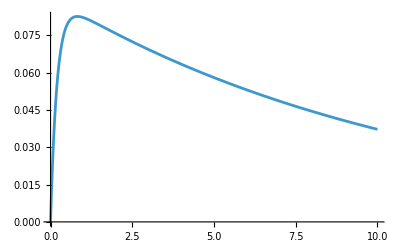

```mathematica
Plot[With[{c=0.1, kboff=0.888,konb=5 }, Evaluate[p1[c]]], {t, 0,10}]
```

```mathematica
pspec = (c*kb)^2*t*Exp[-c*kb*t]
```

c^2 ⅇ^(-c kb t) kb^2 t

```mathematica
FullSimplify[D[Log[pspec],{c,2}]]
```

-2/c^2

```mathematica
secder =FullSimplify[D[Log[p1[c]],{c,2}]]
```

-1/c^2+kboff^2 (1/(-c kboff+konb)^2-(ⅇ^((c kboff+konb) t) t^2)/((ⅇ^(c kboff t)-ⅇ^(konb t))^2))

```mathematica
secderP = FullSimplify[secder*p1[c]]
```

-(c (ⅇ^(-c kboff t)-ⅇ^(-konb t)) kboff konb (-1/c^2+kboff^2 (1/(-c kboff+konb)^2-(ⅇ^((c kboff+konb) t) t^2)/((ⅇ^(c kboff t)-ⅇ^(konb t))^2))))/(c kboff-konb)

```mathematica
secder= FullSimplify[D[Log[p[c]],{c,2}]]
```

(kbon^2 ((c kbon+koffu)^2+2 (c kbon+3 koffu) kuon+kuon^2+ⅇ^(2 √(-4 koffu kuon+(c kbon+koffu+kuon)^2) t) ((c kbon+koffu)^2+2 (c kbon+3 koffu) kuon+kuon^2)+2 koffu kuon √(-4 koffu kuon+(c kbon+koffu+kuon)^2) t-2 ⅇ^(2 √(-4 koffu kuon+(c kbon+koffu+kuon)^2) t) koffu kuon √(-4 koffu kuon+(c kbon+koffu+kuon)^2) t-ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t) (2 ((c kbon+koffu)^2+2 (c kbon+3 koffu) kuon+kuon^2)+(c kbon+koffu+kuon)^2 ((c kbon+koffu)^2+2 (c kbon-koffu) kuon+kuon^2) t^2)))/((-1+ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t))^2 (-4 koffu kuon+(c kbon+koffu+kuon)^2)^2)

```mathematica
secdersimpl = FullSimplify[%,{A==koffu kuon,B==c kbon+koffu+kuon,D==-4 koffu kuon+(c kbon+koffu+kuon)^2}]
```

(kbon^2 (4 (8 A+D)-8 A √D t Coth[(√D t)/2]-D (4 A+D) t^2 Csch[(√D t)/2]^2))/(4 D^2)

```mathematica
FullSimplify[secdersimpl*psimpl]
```

-(A ⅇ^(-1/2 (B+√D) t) (-1+ⅇ^(√D t)) kbon^2 (-4 (8 A+D)+8 A √D t Coth[(√D t)/2]+D (4 A+D) t^2 Csch[(√D t)/2]^2))/(4 D^(5/2))

```mathematica
Expand[%]
```

-(8 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2)/D^(5/2)-(A ⅇ^(-1/2 (B+√D) t) kbon^2)/D^(3/2)+(8 A^2 ⅇ^(-1/2 (B+√D) t+√D t) kbon^2)/D^(5/2)+(A ⅇ^(-1/2 (B+√D) t+√D t) kbon^2)/D^(3/2)+(2 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t Coth[(√D t)/2])/D^2-(2 A^2 ⅇ^(-1/2 (B+√D) t+√D t) kbon^2 t Coth[(√D t)/2])/D^2+(A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Csch[(√D t)/2]^2)/D^(3/2)+(A ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Csch[(√D t)/2]^2)/(4 √D)-(A^2 ⅇ^(-1/2 (B+√D) t+√D t) kbon^2 t^2 Csch[(√D t)/2]^2)/D^(3/2)-(A ⅇ^(-1/2 (B+√D) t+√D t) kbon^2 t^2 Csch[(√D t)/2]^2)/(4 √D)

```mathematica
Integrate[(A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Csch[(√D t)/2]^2)/D^(3/2),t]
```

-1/((B+√D)^2 D^2)2 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 ((B+√D) t ((B+√D) t (-1+Coth[(√D t)/2])+2 (-4+B t+√D t) Hypergeometric2F1[1,-1/2-B/(2 √D),1/2-B/(2 √D),ⅇ^(√D t)])+8 (-2+B t+√D t) HypergeometricPFQ[{1,-1/2-B/(2 √D),-1/2-B/(2 √D)},{1/2-B/(2 √D),1/2-B/(2 √D)},ⅇ^(√D t)]+16 HypergeometricPFQ[{1,-1/2-B/(2 √D),-1/2-B/(2 √D),-1/2-B/(2 √D)},{1/2-B/(2 √D),1/2-B/(2 √D),1/2-B/(2 √D)},ⅇ^(√D t)])

```mathematica
Expand[%]
```

(2 A^2 B^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2)/((B+√D)^2 D^2)+(4 A^2 B ⅇ^(-1/2 (B+√D) t) kbon^2 t^2)/((B+√D)^2 D^(3/2))+(2 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2)/((B+√D)^2 D)-(2 A^2 B^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Coth[(√D t)/2])/((B+√D)^2 D^2)-(4 A^2 B ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Coth[(√D t)/2])/((B+√D)^2 D^(3/2))-(2 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Coth[(√D t)/2])/((B+√D)^2 D)+(16 A^2 B ⅇ^(-1/2 (B+√D) t) kbon^2 t Hypergeometric2F1[1,-1/2-B/(2 √D),1/2-B/(2 √D),ⅇ^(√D t)])/((B+√D)^2 D^2)+(16 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t Hypergeometric2F1[1,-1/2-B/(2 √D),1/2-B/(2 √D),ⅇ^(√D t)])/((B+√D)^2 D^(3/2))-(4 A^2 B^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Hypergeometric2F1[1,-1/2-B/(2 √D),1/2-B/(2 √D),ⅇ^(√D t)])/((B+√D)^2 D^2)-(8 A^2 B ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Hypergeometric2F1[1,-1/2-B/(2 √D),1/2-B/(2 √D),ⅇ^(√D t)])/((B+√D)^2 D^(3/2))-(4 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t^2 Hypergeometric2F1[1,-1/2-B/(2 √D),1/2-B/(2 √D),ⅇ^(√D t)])/((B+√D)^2 D)+(32 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 HypergeometricPFQ[{1,-1/2-B/(2 √D),-1/2-B/(2 √D)},{1/2-B/(2 √D),1/2-B/(2 √D)},ⅇ^(√D t)])/((B+√D)^2 D^2)-(16 A^2 B ⅇ^(-1/2 (B+√D) t) kbon^2 t HypergeometricPFQ[{1,-1/2-B/(2 √D),-1/2-B/(2 √D)},{1/2-B/(2 √D),1/2-B/(2 √D)},ⅇ^(√D t)])/((B+√D)^2 D^2)-(16 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 t HypergeometricPFQ[{1,-1/2-B/(2 √D),-1/2-B/(2 √D)},{1/2-B/(2 √D),1/2-B/(2 √D)},ⅇ^(√D t)])/((B+√D)^2 D^(3/2))-(32 A^2 ⅇ^(-1/2 (B+√D) t) kbon^2 HypergeometricPFQ[{1,-1/2-B/(2 √D),-1/2-B/(2 √D),-1/2-B/(2 √D)},{1/2-B/(2 √D),1/2-B/(2 √D),1/2-B/(2 √D)},ⅇ^(√D t)])/((B+√D)^2 D^2)

```mathematica
integrand1[t]:=FullSimplify[secder1*p1[c]]
```

```mathematica
integrand1[t]
```

-(c (ⅇ^(-c kboff t)-ⅇ^(-konb t)) kboff konb (-1/c^2+kboff^2 (1/(-c kboff+konb)^2-(ⅇ^((c kboff+konb) t) t^2)/((ⅇ^(c kboff t)-ⅇ^(konb t))^2))))/(c kboff-konb)

```mathematica
int1[t]:=Integrate[integrand1[t],t]
```

```mathematica
integrand=FullSimplify[secder*p[c]]
```

secder p[c]

```mathematica
int[t] :=Integrate[integrand[t],t]
```

```mathematica
FullSimplify[With[{t=0}, Evaluate[int[t]]]]
```

(kbon^2 (((c kbon+koffu)^2+2 (c kbon-3 koffu) kuon+kuon^2) ((c kbon+koffu)^2+2 (c kbon-koffu) kuon+kuon^2)-koffu kuon (c kbon+koffu+kuon)^2 PolyGamma[2,(-c kbon-koffu-kuon+√(-4 koffu kuon+(c kbon+koffu+kuon)^2))/(2 √(-4 koffu kuon+(c kbon+koffu+kuon)^2))]))/(-4 koffu kuon+(c kbon+koffu+kuon)^2)^3

```mathematica
integrand[t]
```

-((ⅇ^(1/2 (-c kbon-koffu-kuon+√(-4 koffu kuon+(c kbon+koffu+kuon)^2)) t) kbon^2 koffu kuon (2 ((c kbon+koffu)^2+2 (c kbon+3 koffu) kuon+kuon^2)+(c kbon+koffu+kuon)^2 (-4 koffu kuon+(c kbon+koffu+kuon)^2) t^2-2 ((c kbon+koffu)^2+2 (c kbon+3 koffu) kuon+kuon^2) Cosh[√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t]+4 koffu kuon √(-4 koffu kuon+(c kbon+koffu+kuon)^2) t Sinh[√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t]))/((-1+ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t)) (-4 koffu kuon+(c kbon+koffu+kuon)^2)^(5/2)))

```mathematica
V[kb]:=(c*kb*kon)/(c*kb+kon)*kon^2/(kon^2+c^2*kb^2)
```

```mathematica
dV = FullSimplify[D[V[kb],{kb,1}]]
```

(c kon^3 (-2 c^3 kb^3-c^2 kb^2 kon+kon^3))/((c kb+kon)^2 (c^2 kb^2+kon^2)^2)

```mathematica
With[{kon=5},Evaluate[Solve[2 c^3 kb^3+c^2 kb^2 kon*(2-kon^2)-kon^5==0,kb]]]
```

{{kb→115/(6 c)+(13225 c)/(6 (1689625 c^6+3750 √38526 √(c^12))^(1/3))+((1689625 c^6+3750 √38526 √(c^12))^(1/3))/(6 c^3)},{kb→115/(6 c)-(13225 (1+ⅈ √3) c)/(12 (1689625 c^6+3750 √38526 √(c^12))^(1/3))-((1-ⅈ √3) (1689625 c^6+3750 √38526 √(c^12))^(1/3))/(12 c^3)},{kb→115/(6 c)-(13225 (1-ⅈ √3) c)/(12 (1689625 c^6+3750 √38526 √(c^12))^(1/3))-((1+ⅈ √3) (1689625 c^6+3750 √38526 √(c^12))^(1/3))/(12 c^3)}}

```mathematica
Int=Integrate[t^2/(ⅇ^(a*t)-ⅇ^(b*t)),t]
```

(b ⅇ^(-a t) (2+2 a t+a^2 t^2))/(a^3 (a-b))+1/(a^3 (a-b))ⅇ^(-a t) (-2 b-2 a b t-a^2 b t^2-a^3 t^2 Hypergeometric2F1[1,a/(a-b),2+b/(a-b),ⅇ^((-a+b) t)]+a^2 b t^2 Hypergeometric2F1[1,a/(a-b),2+b/(a-b),ⅇ^((-a+b) t)]+2 a (-a+b) t HypergeometricPFQ[{1,a/(a-b),a/(a-b)},{2+b/(a-b),2+b/(a-b)},ⅇ^((-a+b) t)]-2 (a-b) HypergeometricPFQ[{1,a/(a-b),a/(a-b),a/(a-b)},{2+b/(a-b),2+b/(a-b),2+b/(a-b)},ⅇ^((-a+b) t)])

```mathematica
With[{t=0},Evaluate[Int]]
```

(2 b)/(a^3 (a-b))+(-2 b-2 (a-b) HypergeometricPFQ[{1,a/(a-b),a/(a-b),a/(a-b)},{2+b/(a-b),2+b/(a-b),2+b/(a-b)},1])/(a^3 (a-b))

```mathematica
FullSimplify[%]
```

-(2 HypergeometricPFQ[{1,a/(a-b),a/(a-b),a/(a-b)},{2+b/(a-b),2+b/(a-b),2+b/(a-b)},1])/a^3

```mathematica
V = kb^2/(kon-c*kb)^2+(2*c*(kb^3)*kon /(kon-c*kb)^4 )* HurwitzZeta[3,c*kb/(c*kb-kon)];
```

```mathematica
tau = (c*kb+kon)/(c*kb*kon)
```

(c kb+kon)/(c kb kon)

```mathematica
D[V/tau,kb]
```

-(c^2 kb kon (kb^2/(-c kb+kon)^2+(2 c kb^3 kon HurwitzZeta[3,(c kb)/(c kb-kon)])/(-c kb+kon)^4))/(c kb+kon)^2+(c kon (kb^2/(-c kb+kon)^2+(2 c kb^3 kon HurwitzZeta[3,(c kb)/(c kb-kon)])/(-c kb+kon)^4))/(c kb+kon)+1/(c kb+kon)c kb kon ((2 c kb^2)/(-c kb+kon)^3+(2 kb)/(-c kb+kon)^2+(8 c^2 kb^3 kon HurwitzZeta[3,(c kb)/(c kb-kon)])/(-c kb+kon)^5+(6 c kb^2 kon HurwitzZeta[3,(c kb)/(c kb-kon)])/(-c kb+kon)^4-(6 c kb^3 (-(c^2 kb)/(c kb-kon)^2+c/(c kb-kon)) kon HurwitzZeta[4,(c kb)/(c kb-kon)])/(-c kb+kon)^4)

```mathematica
-((c kb-2 kon) (-c kb+kon)^4)+c kb kon ((c kb-kon) (c kb+3 kon) PolyGamma[2,(c kb)/(c kb-kon)]+c kb kon PolyGamma[3,(c kb)/(c kb-kon)])
```

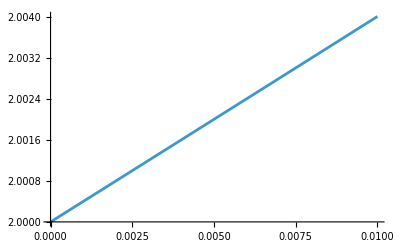

```mathematica
Plot[{HurwitzZeta[3,ckb/(5-ckb)]*(10/ckb)*(ckb/(5-ckb))^4},{ckb,0,0.01}]
```

```mathematica
HurwitzZeta[3,1]
```

Zeta[3]

(c kb+kon)/(c kb kon)

```mathematica
Voverdc2 = (1/c^2 - (kb/(c*kb-kon))^2)/(2*tau)
```

(1/c^2-kb^2/(c kb-kon)^2)/(2 tau)

```mathematica
FullSimplify[D[Voverdc2, kb]]
```

(kb kon)/((c kb-kon)^3 tau)

```mathematica
(*MoM estimator for the off time*)
Solve[2(tauon+1/konb)x^3+x^2-konb^2 ==0, x]
```

{{x→-konb/(6 (1+konb tauon))+konb^2/(3 2^(2/3) (1+konb tauon) (106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3))+((106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3))/(6 2^(1/3) (1+konb tauon))},{x→-konb/(6 (1+konb tauon))-((1+ⅈ √3) konb^2)/(6 2^(2/3) (1+konb tauon) (106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3))-1/(12 2^(1/3) (1+konb tauon))(1-ⅈ √3) (106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3)},{x→-konb/(6 (1+konb tauon))-((1-ⅈ √3) konb^2)/(6 2^(2/3) (1+konb tauon) (106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3))-1/(12 2^(1/3) (1+konb tauon))(1+ⅈ √3) (106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3)}}

```mathematica
With[{tauon=tau, konb=l}, Evaluate[-konb/(6 (1+konb tauon))+konb^2/(3 2^(2/3) (1+konb tauon) (106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3))+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2+√(-4 konb^6+(106 konb^3+216 konb^4 tauon+108 konb^5 tauon^2)^2))^(1/3)/(6 2^(1/3) (1+konb tauon))]]
```

-l/(6 (1+l tau))+l^2/(3 2^(2/3) (1+l tau) (106 l^3+216 l^4 tau+108 l^5 tau^2+√(-4 l^6+(106 l^3+216 l^4 tau+108 l^5 tau^2)^2))^(1/3))+(106 l^3+216 l^4 tau+108 l^5 tau^2+√(-4 l^6+(106 l^3+216 l^4 tau+108 l^5 tau^2)^2))^(1/3)/(6 2^(1/3) (1+l tau))

```mathematica
FullSimplify[%]
```

1/(6 (1+l tau))((6 √3 √(l^6 (1+l tau)^2 (26+27 l tau (2+l tau)))+l^3 (53+54 l tau (2+l tau)))^(1/3)+l (-1+l/(6 √3 √(l^6 (1+l tau)^2 (26+27 l tau (2+l tau)))+l^3 (53+54 l tau (2+l tau)))^(1/3)))

```mathematica
A := ku+koff+x
tau := 1/koff + 1/ku + x/(koff*ku)+1/(ckboff)+1/kon
```

```mathematica
Solve[2(tau*A^2-2*tau*ku*koff)==x*(A^2/(koff*ku)+2*tau*A-2), x];
```

```mathematica
With[{ku=5, koff=5,kon=5,ckboff=2.2}, Evaluate[%]]
```

{{x→-21.2948+8.88178×10^-15 ⅈ},{x→26.0478+4.44089×10^-15 ⅈ},{x→-4.75292-1.24345×10^-14 ⅈ}}

```mathematica
With[{c0=1,kb=0.0888, kon=5},NSolve[c*kb*(c*kb-kon)*toff ==kon*(Exp[(c*kb-kon)*toff]-1), c ]]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[0.0888 (-5+0.0888 c) c (1/(c0 kb)+1/kon)==5 (-1+ⅇ^((-5+0.0888 c) (1/(c0 kb)+1/kon))),c]

```mathematica
InverseLaplaceTransform[(a/(s+a+c*b))(1-c*b/((s+a+c*b)(s+d))), s, t]
```

a (((a^2+b c+2 a b c+b^2 c^2-2 a d-2 b c d+d^2) ⅇ^(-((a+b c) t)))/(a+b c-d)^2-(b c ⅇ^(-d t))/(a+b c-d)^2+(b c ⅇ^(-((a+b c) t)) t)/(a+b c-d))

```mathematica
Simplify[%]
```

(a ⅇ^(-((a+b c+d) t)) ((a-d)^2 ⅇ^(d t)+b^2 c^2 ⅇ^(d t) (1+t)-b c (ⅇ^((a+b c) t)+ⅇ^(d t) (-1-a (2+t)+d (2+t)))))/(a+b c-d)^2